# In-Class Demo (01-11-2022)

## Exploring y'(t) = f(y) with f(y) = y^3-y

### Defining the function f(t) = y^3-y

The following line of code defines the function f(y) = y^3-y.  In Mathematica, when you define a function that has an input, you need to use the underscore in the definition as shown below.

```mathematica
f[y_]=y^3-y
```

-y+y^3

### Using DSolve to Symbolically Solve the Differential Equation

The DSolve function symbolically solves the differential equation with the dependent variable y[t], and independent variable t.  Note the use of the double equal sign.

```mathematica
DSolve[y'[t]==f[y[t]],y[t],t]
```

{{y[t]→-1/(√(1+ⅇ^(2 t+2 C[1])))},{y[t]→1/(√(1+ⅇ^(2 t+2 C[1])))}}

#### Solving Initial Value Problems Symbolically

If we would like to include initial conditions, say, y(0) = 1, then we need to solve the initial value problem.  Remember that the initial value problem requires that we find y(t) that satisfies  y' = y^3- y along with y(0) = 1. Thus, we have to provide DSolve with a list of equations to be satisfied as {y’[t]==y[t]^3 - y[t], y[0]==1}

```mathematica
DSolve[{y'[t]==y[t]^3-y[t],y[0]==1},y[t],t]
```

{{y[t]→1}}

We can also have Mathematica solve all initial value problems so that we can plot the solution as we vary the initial starting value.  To do this, we will create a function called sol[α_] that will take α as a parameter to solve the IVP y' = y^3-y, y(0) = α. 

Note: In the code below, we specifically use the := symbol when defining the function sol[α_]:=DSolve[...].  What this does is prevent Mathematica from solving the differential equation until we substitute the value of α into the differential equation.  Had we simply used the = symbol, Mathematica would solve the IVP in terms of α and then attempt to plug in the value of α afterwards.  This could lead to an unexpected divide by zero error.

```mathematica
sol[α_]:=DSolve[{y'[t]==y[t]^3-y[t],y[0]==α},y[t],t]
```

Now we can test out our function.  Let’s solve a few different initial value problems with y(0) = -1, y(0) = 1/2, and y(0) = 5/4

```mathematica
sol[-1]
sol[1/2]
sol[5/4]
```

{{y[t]→-1}}

{{y[t]→1/(√(1+3 ⅇ^(2 t)))}}

{{y[t]→5/(√(25-9 ⅇ^(2 t)))}}

If we now wanted to plot the solution to the IVP with y(0) = 1/2 for 0≤ t ≤5, we would simply use the command: Plot[Evaluate[y[t]/.sol[1/2]],{t,0,5}].  The following is a simple breakdown on the commands involved:

y[t]/.sol[1/2] says “for the function y[t], use the substitution rule given provided by sol[1/2].  Remember, sol[1/2] is simply {{y[t]→1/(√(1+3 ⅇ^(2 t)))}} 

Evaluate[...] says evaluate the expression inside at specific t values.

Plot[...,{t,0,5}] says plot the function for t = 0  through t = 5

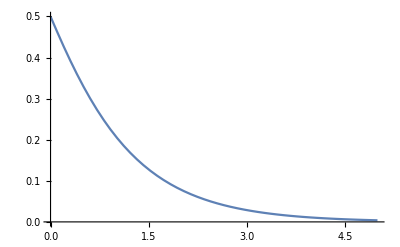

```mathematica
Plot[Evaluate[y[t]/.sol[1/2]],{t,0,5}]
```

We could also create a table of solutions for initial conditions starting from y(0) = -6/5 increasing up to y(0) = 6/5 by increments of 1/5 as follows (notice, we are going to store this list of solutions in a variable named sols

```mathematica
sols=Table[sol[α],{α,-6/5,6/5,1/5}]
```

{{{y[t]→-6/(√(36-11 ⅇ^(2 t)))}},{{y[t]→-1}},{{y[t]→-4/(√(16+9 ⅇ^(2 t)))}},{{y[t]→-3/(√(9+16 ⅇ^(2 t)))}},{{y[t]→-2/(√(4+21 ⅇ^(2 t)))}},{{y[t]→-1/(√(1+24 ⅇ^(2 t)))}},{{y[t]→0}},{{y[t]→1/(√(1+24 ⅇ^(2 t)))}},{{y[t]→2/(√(4+21 ⅇ^(2 t)))}},{{y[t]→3/(√(9+16 ⅇ^(2 t)))}},{{y[t]→4/(√(16+9 ⅇ^(2 t)))}},{{y[t]→1}},{{y[t]→6/(√(36-11 ⅇ^(2 t)))}}}

Now we can plot all of these solutions on the same graph by substituting in our list of solutions to the function y(t) as follows

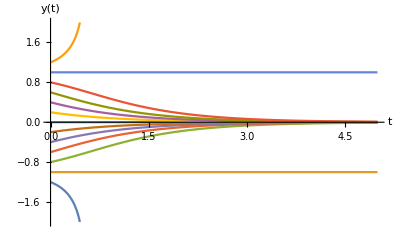

```mathematica
Plot[
Evaluate[y[t]/.sols],{t,0,5},
PlotRange->{-2,2},AxesLabel->{t,y[t]}
]
```

#### Comparing with Phase Lines

```mathematica
eqPts = Solve[f[y]==0,y] (* Solve for the equilibrium points symbolically!*)
```

{{y→-1},{y→0},{y→1}}

Now, we can plot y'(t) vs y(t) as well as the equilibrium points that we found earlier!

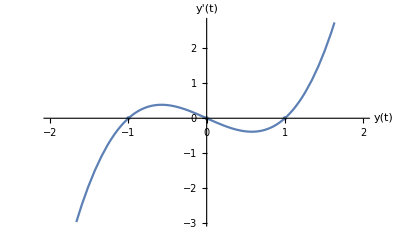

```mathematica
eqPtPlot=ListPlot[{y,f[y]}/.eqPts,PlotStyle->{PointSize[Large]}];
pLPlot=Plot[f[y],{y,-2,2}];
Show[pLPlot,eqPtPlot,AxesLabel->{y[t],y'[t]}]
```